```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6a *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,21}];
simq=Table[{},{i,1,21}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
SeedRandom[7];
```

```mathematica
(* Run simulation *)
Do[
results=RunSimulationCheckEachMutation2[10^(4+((j-1)/5)),Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,10^(4+((j-1)/5))/popsize genotypeabundances][[2]][[1]];
simv[[j]]={(4+((j-1)/5)),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]};
simq[[j]]={(4+((j-1)/5)),Mean[results[[;;,9]]]/Δc1};
,{j,1,21}];
thryvest=Table[{(4+(j/25)),(10^5 Δc1^2(2 Log[Δc1 10^(4+(j/25))]-Log[Δc1/U1]))/Log[Δc1/U1]^2},{j,0,100}];
thryvext=Table[{(4+(j/25)),10^5 getTransV[Δc1,U1,10^(4+(j/25)),True]},{j,0,100}];
thryqest=Table[{(4+(j/25)),2((4+((j-1)/25))-2)/3},{j,0,100}];
thryqext=Table[{(4+(j/25)),getTransQ[Δc1,U1,10^(4+(j/25)),True]},{j,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp006.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

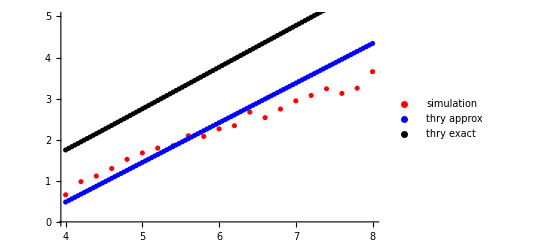

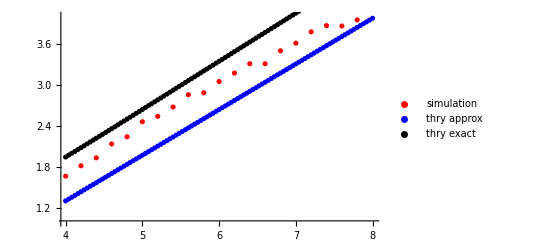

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp006.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,5}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1,4}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 b *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-4,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,21}];
simq=Table[{},{i,1,21}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
SeedRandom[7];
```

```mathematica
(* Run simulation *)
Do[
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,10^(-4-((j-1)/10)),U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
simv[[j]]={(-4-((j-1)/10)),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]};
simq[[j]]={(-4-((j-1)/10)),Mean[results[[;;,9]]]/Δc1};
,{j,1,21}];
thryvest=Table[{(-4-(i/50)),(10^5 Δc1^2(2 Log[popsize Δc1]-Log[Δc1/10^(-4-(i/50))]))/(Log[Δc1/10^(-4-(i/50))]^2)},{i,0,100}];
thryvext=Table[{(-4-(i/50)),10^5 getTransV[Δc1,10^(-4-(i/50)),popsize,True]},{i,0,100}];
thryqest=Table[{(-4-(i/50)),-8/((-4-(i/50))+2)},{i,0,100}];
thryqext=Table[{(-4-(i/50)),getTransQ[Δc1,10^(-4-(i/50)),popsize,True]},{i,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp007.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

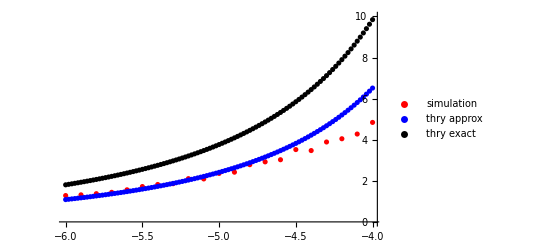

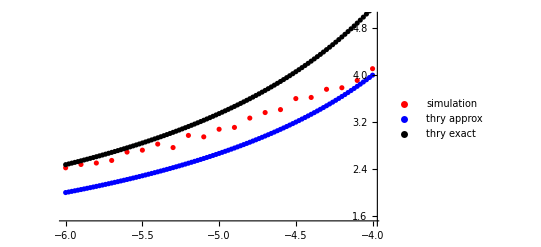

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp007.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,10}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1.5,5}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 c *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,21}];
simq=Table[{},{i,1,21}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
SeedRandom[7];
```

```mathematica
(* Run simulation *)
Do[
results=RunSimulationCheckEachMutation2[popsize,10^(-13/4+(j-1)/10),Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
simv[[j]]={(-13/4+(j-1)/10),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]};
simq[[j]]={(-13/4+(j-1)/10),Mean[results[[;;,9]]]/10^(-13/4+(j-1)/10)};
,{j,1,21}];
thryvest=Table[{(-13/4+(i/50)),(10^5 10^(2(-13/4+i/50))(2 Log[popsize 10^(-13/4+i/50)]-Log[10^(-13/4+i/50)/U1]))/(Log[10^(-13/4+i/50)/U1]^2)},{i,0,100}];
thryvext=Table[{(-13/4+(i/50)),10^5 getTransV[10^(-13/4+i/50),U1,popsize,True]},{i,0,100}];
thryqest=Table[{(-13/4+(i/50)),(2 Log[popsize 10^(-13/4+i/50)])/Log[10^(-13/4+i/50)/U1]},{i,0,100}];
thryqext=Table[{(-13/4+(i/50)),getTransQ[10^(-13/4+i/50),U1,popsize,True]},{i,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-vary_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp008.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

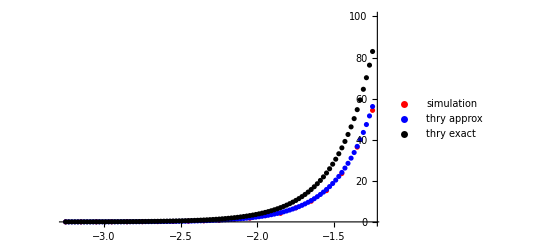

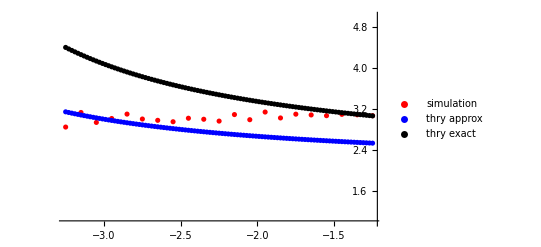

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-vary_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp008.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,100}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1,5}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 c *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.001,0.00,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={1,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={1,False,False,False};
(* Set initial genotypes and their abundances *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,False];
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
SeedRandom[7];
```

Trait 1 q = 3. in Concurrent Mutations Regime with expected time scale 2302.59 and rate of adaptation 4.34294×10^-7

Trait 2 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 a Examine Statistical Spread*)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,210}];
simq=Table[{},{i,1,210}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
```

```mathematica
(* Run simulation *)
simdata =ParallelTable[
results=RunSimulationCheckEachMutation2[10^(4+((Mod[j,21,1]-1)/5)),Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,10^(4+((Mod[j,21,1]-1)/5))/popsize genotypeabundances][[2]][[1]];
{{(4+((Mod[j,21,1]-1)/5)),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]},{(4+((Mod[j,21,1]-1)/5)),Mean[results[[;;,9]]]/Δc1}}
,{j,1,210}];
simv=simdata[[;;,1]];
simq=simdata[[;;,2]];
```

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp010.m"];
thryvest=Table[{(4+(j/25)),(10^5 Δc1^2(2 Log[Δc1 10^(4+(j/25))]-Log[Δc1/U1]))/Log[Δc1/U1]^2},{j,0,100}];
thryvext=Table[{(4+(j/25)),10^5 getTransV[Δc1,U1,10^(4+(j/25)),True]},{j,0,100}];
thryqest=Table[{(4+(j/25)),2((4+((j-1)/25))-2)/3},{j,0,100}];
thryqext=Table[{(4+(j/25)),getTransQ[Δc1,U1,10^(4+(j/25)),True]},{j,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp010.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

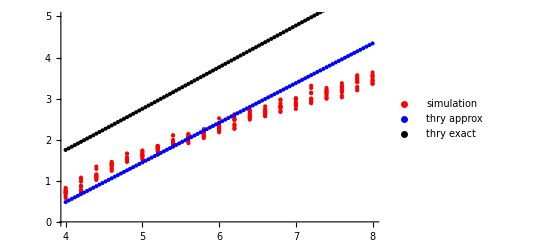

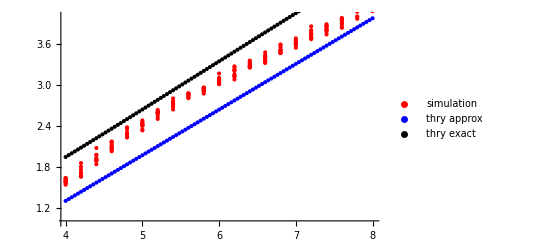

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp010.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,5}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1,4}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 b *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-4,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,210}];
simq=Table[{},{i,1,210}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
```

```mathematica
(* Run simulation *)
simdata=ParallelTable[
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,10^(-4-((Mod[j,21,1]-1)/10)),U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
{{(-4-((Mod[j,21,1]-1)/10)),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]},{(-4-((Mod[j,21,1]-1)/10)),Mean[results[[;;,9]]]/Δc1}}
,{j,1,210}];
simv=simdata[[;;,1]];
simq=simdata[[;;,2]];
```

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp011.m"];
thryvest=Table[{(-4-(i/50)),(10^5 Δc1^2(2 Log[popsize Δc1]-Log[Δc1/10^(-4-(i/50))]))/(Log[Δc1/10^(-4-(i/50))]^2)},{i,0,100}];
thryvext=Table[{(-4-(i/50)),10^5 getTransV[Δc1,10^(-4-(i/50)),popsize,True]},{i,0,100}];
thryqest=Table[{(-4-(i/50)),-8/((-4-(i/50))+2)},{i,0,100}];
thryqext=Table[{(-4-(i/50)),getTransQ[Δc1,10^(-4-(i/50)),popsize,True]},{i,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp011.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

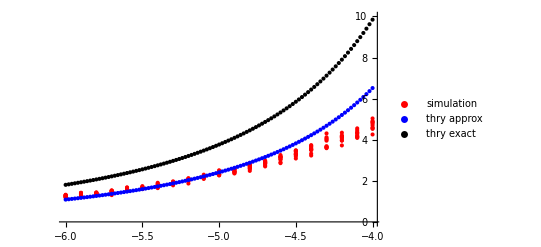

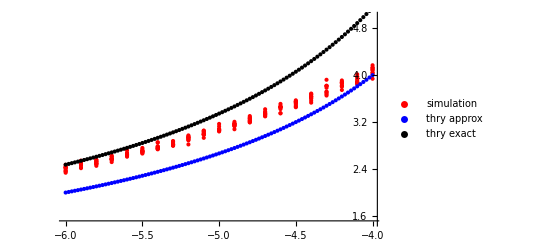

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp011.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,10}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1.5,5}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 c *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,210}];
simq=Table[{},{i,1,210}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
```

```mathematica
(* Run simulation *)
simdata=ParallelTable[
results=RunSimulationCheckEachMutation2[popsize,10^(-13/4+(Mod[j,21,1]-1)/10),Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
{{(-13/4+(Mod[j,21,1]-1)/10),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]},{(-13/4+(Mod[j,21,1]-1)/10),Mean[results[[;;,9]]]/10^(-13/4+(Mod[j,21,1]-1)/10)}}
,{j,1,210}];
simv=simdata[[;;,1]];
simq=simdata[[;;,2]];
```

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-vary_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp012.m"];
thryvest=Table[{(-13/4+(i/50)),(10^5 10^(2(-13/4+i/50))(2 Log[popsize 10^(-13/4+i/50)]-Log[10^(-13/4+i/50)/U1]))/(Log[10^(-13/4+i/50)/U1]^2)},{i,0,100}];
thryvext=Table[{(-13/4+(i/50)),10^5 getTransV[10^(-13/4+i/50),U1,popsize,True]},{i,0,100}];
thryqest=Table[{(-13/4+(i/50)),(2 Log[popsize 10^(-13/4+i/50)])/Log[10^(-13/4+i/50)/U1]},{i,0,100}];
thryqext=Table[{(-13/4+(i/50)),getTransQ[10^(-13/4+i/50),U1,popsize,True]},{i,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-vary_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp012.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

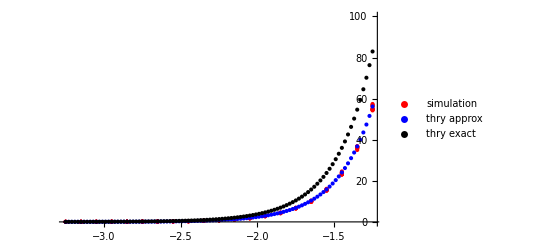

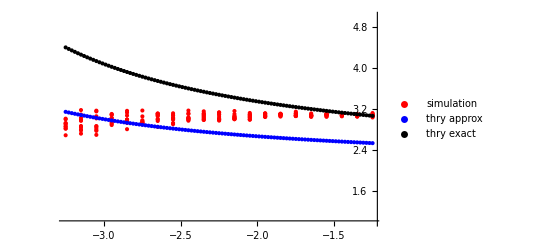

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-vary_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp012.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,100}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1,5}]
```

```mathematica
(* ------------------------------------------------------------------------------------------------------------ *)
(* ------------------------------------------------------------------------------------------------------------ *)
(* ------------------------------------------------------------------------------------------------------------ *)
(* Code to Test and Debug mutation modules *)

(* Set parameters for simulation of taus *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-4,0 10^-4,10^7};
{starttime,timestep,maxtime,globaltime}={0,(50 Log[Δc1/U1]^2)/(Δc1(2Log[popsize Δc1]-Log[Δc1/U1])),(50 Log[Δc1/U1]^2)/(Δc1(2Log[popsize Δc1]-Log[Δc1/U1])),0}; 
{verbose,veryverbose,time1,time2,time3,time4}={False,False,{0,0},{0,0},{0,0},{0,0}};
genotypes ={{1,0},{2,0}};
genotypeabundances={popsize-1/Δc1,1/Δc1};
meanFit = genotypes;
{system,sol}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
(* Sample the tau's to compare with theoretical distribution *)
taus = ParallelTable[
(* asdf *)
NextMutation[popsize,Δc1,Δc2,U1,U2,sol,genotypes,genotypeabundances,starttime,timestep][[1]]
(* asdf *)
,{i,1,5000}];
(* rootaddress="C:/Users/dirge/Documents/kgrel2d/"; *)
rootaddress="~/Documents/kgrel2d/";
workingfilename="_N-10p07_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp1.m";
Export[rootaddress<>"data/simtest/tauData"<>workingfilename,{taus,sol}];
rootaddress="~/Documents/kgrel2d/";
workingfilename="_N-10p07_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp1.m";
results = Import[rootaddress<>"data/simtest/tauData"<>workingfilename];
taus = results[[1]];
sol = results[[2]];
n0=((U1 ((2Δc1)/(1+2Δc1))n2[t]/.sol[[1]])/.t->#)&;
ni=NDSolveValue[{y'[t]==n0[t],y[0]==0},y,{t,0,1000}];
f[t_]:=(n0[t]Exp[-ni[t]]);
F[t_]:=1-Exp[-ni[t]];
(* Seems like my code is working fine! *)
Show[Histogram[taus,Automatic,"PDF"],Plot[f[t],{t,0,830}]]
Plot[{F[t],1},{t,0,1000}]
```

```mathematica
(* create data file for python using simulations results from set 6 experiment *)
{results,data} = {{},{}};
Do[
results = Import["C:/Users/dirge/Documents/kgrel2d/data/simtest/simtestset6/simtest_data_set2_exp"<>ToString[i]<>".m"];
data = Join[data,results];
,{i,1,93}];
Export["C:/Users/dirge/Documents/kgrel2d/data/pythondata/sumdata_exp6.dat",data];
```

```mathematica
(* create data file for python using simulations results from set 6 experiment *)
{results,NsUparam} = {{},{}};
Do[
results = Import["C:/Users/dirge/Documents/kgrel2d/data/simtest/simtestset6/computationtimes_set2_exp"<>ToString[i]<>".m"];
NsUparam = Join[NsUparam,{results[[6]]}];
,{i,1,93}];
Export["C:/Users/dirge/Documents/kgrel2d/data/pythondata/sumparam_exp6.dat",NsUparam];
```

```mathematica
collectMyData2[globaltime_,genotypes_,genotypeabundances_,Δc1_,Δc2_,stats_]:=Module[
{popsize,ibar,jbar,r1bar,r2bar,vari,varj,covij,var,timeAvgVar1,timeAvgVar2,timeAvgCov,timeAvgVar},

(* COLLECT ALL DATA: {TIMESTAMP, GENOTYPES, GENOTYPEABUNDANCES} *)
popsize = Total[genotypeabundances];
{ibar,jbar}=((1/popsize){genotypeabundances}.genotypes)[[1]];
{r1bar,r2bar}={Δc1,Δc2}*{ibar,jbar};
covij=Δc1 Δc2 Sum[(genotypes[[i]][[1]]-ibar)(genotypes[[i]][[2]]-jbar)(genotypeabundances[[i]]/popsize),{i,1,Length[genotypes]}];
vari=Δc1^2 Sum[(genotypes[[i]][[1]]-ibar)^2(genotypeabundances[[i]]/popsize),{i,1,Length[genotypes]}];
varj=Δc2^2 Sum[(genotypes[[i]][[2]]-jbar)^2(genotypeabundances[[i]]/popsize),{i,1,Length[genotypes]}];
var = vari+varj+2covij;

timeAvgVar1 = stats[[4]](stats[[1]])/globaltime+vari/globaltime;
timeAvgVar2= stats[[5]](stats[[1]])/globaltime+varj/globaltime;
timeAvgCov = stats[[6]](stats[[1]])/globaltime+covij/globaltime;
timeAvgVar= stats[[7]](stats[[1]])/globaltime+var/globaltime;

{globaltime,r1bar,r2bar,timeAvgVar1,timeAvgVar2,timeAvgCov,timeAvgVar}
]
getResultStats[results_,Δc1_,Δc2_]:=Module[{popsize,ibar,jbar,r1bar,r2bar,covij,vari,varj,var,genotypes,genotypeabundances,globaltime,stats},
genotypes=results[[1]][[2]];
genotypeabundances=results[[1]][[3]];
globaltime=results[[1]][[1]];
popsize = Total[genotypeabundances];
{ibar,jbar}=((1/popsize){genotypeabundances}.genotypes)[[1]];
{r1bar,r2bar}={Δc1,Δc2}*{ibar,jbar};
covij=Δc1 Δc2 Sum[(genotypes[[i]][[1]]-ibar)(genotypes[[i]][[2]]-jbar)(genotypeabundances[[i]]/popsize),{i,1,Length[genotypes]}];
vari=Δc1^2 Sum[(genotypes[[i]][[1]]-ibar)^2(genotypeabundances[[i]]/popsize),{i,1,Length[genotypes]}];
varj=Δc2^2 Sum[(genotypes[[i]][[2]]-jbar)^2(genotypeabundances[[i]]/popsize),{i,1,Length[genotypes]}];
var = vari+varj+2covij;
stats = {globaltime,r1bar,r2bar,vari,varj,covij,var};

Do[
If[Mod[results[[i]][[1]],1]==0,
stats=collectMyData2[results[[i]][[1]],results[[i]][[2]],results[[i]][[3]],Δc1,Δc2,stats];]
,{i,2,Length[results]}];
{stats}
]
```

```mathematica
(* Process simulation data for python *)
ParallelDo[ 
parameters = Import["~/Documents/kgrel2d/data/simtest/simtestset9/computationtimes_set1_exp"<>ToString[i]<>".m"][[6]];
results=Import["~/Documents/kgrel2d/data/simtest/simtestset9/simtest_initpop_set1_exp"<>ToString[i]<>".m"];
stats = getResultStats[results,parameters[[2]],parameters[[2]]];
time3=AbsoluteTime[];
Print["Experiment "<>ToString[i]<>" required ",(time2-time1)/60," minutes to import and ", (time3-time2)/60," minutes to process."];
initpop = {stats,results[[-1]][[2]],results[[-1]][[3]]};
Export["~/Documents/kgrel2d/data/simtest/simtestset5/python_exp"<>ToString[i]<>".m",initpop];
,{i,1,33}];
```

```mathematica
parameters = Import["~/Documents/kgrel2d/data/simtest/simtestset9/computationtimes_set1_exp1.m"];
results=Import["~/Documents/kgrel2d/data/simtest/simtestset9/simtest_initpop_set1_exp1.m"];
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {{19.5,3.718567180011119×10^9},{9439.11,3.718567180012451×10^9},{653.85,3.718567179974169×10^9},{11673.05081,3.718555507249799×10^9},8486,parameters}.

```mathematica
parameters
results
```

parameters

{{{2.×10^6,1.08933,1.04783,1.30947×10^-6,1.28881×10^-6,-7.67105×10^-7,1.06407×10^-6},{{948,909},{949,908},{947,910},{948,910},{949,909},{947,911},{950,908},{950,909},{949,910},{948,911},{947,912},{948,912},{950,910},{951,908},{949,912},{948,913},{949,911},{951,909},{947,913},{951,910},{950,911},{948,914},{949,913},{950,912},{951,911},{952,909},{952,910},{950,913},{952,911},{948,915},{951,912},{949,914},{952,912},{950,914},{951,913},{953,911}},{23.3504,39.6131,20.7942,1365.46,1862.32,1162.65,124.528,39240.9,51186.9,9669.48,16168.2,2.89867×10^7,221406.,24.6874,8.03451×10^6,7.11171×10^6,118323.,23042.2,18459.3,539567.,66266.,2.24655×10^6,567292.,1.03795×10^6,473799.,39325.,49464.5,222398.,91123.,6889.3,18856.3,3334.93,796.566,782.358,261.443,281.704}}}

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* MULTIPLE PARAMETER SIMULATION SCRIPT - Initialize populations parameters and data processing options *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
{s,U,popsize,starttime,timestep,maxtime}={0.01,1 10^-5,5 10^7,0,1000,2000000};
{verbose,veryverbose}={False,False};
{genotypes,genotypeabundances}=getInitial2Ddistribution[5,popsize,s,s,U,U];
{windowsaddress,ubuntuaddress}={"C:/Users/Kevin/Documents/kgrel2d/","~/Documents/kgrel2d/"};
rootaddress=ubuntuaddress;
(*first array set exp 5 and exp 7 (exp 5 cont)*)
arrys = Table[1 10^(-3+i Log10[4]/10),{i,1,10}];
arryU =Table[10^(-6+i Log10[4]/10),{i,1,10}];
arryN=Table[5 10^(6+i Log10[20]/10),{i,1,20}];
{a1,a2,a3} = {Length[arrys],Length[arryU],Length[arryN]};
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
ParallelDo[
{myseed,time1,time2,time3,time4}={RandomInteger[{1,10000}],{0,0},{0,0},{0,0},{0,0}};
SeedRandom[myseed];
parameterCase=Which[1≤ i≤a1,1,a1+1≤ i≤a1+a2,2,a1+a2+1≤ i≤ a1+a2+a3,3];
indxadj=Which[1≤ i≤a1,0,a1+1≤ i≤a1+a2,a1,a1+a2+1≤ i≤ a1+a2+a3,a1+a2];
Print[ToString[i]]
Which[
parameterCase==1,
parameters = Import[rootaddress<>"data/simtest/simtestset9/computationtimes_set1_exp"<>ToString[i]<>".m"];
parameters[[6]]={popsize,arrys[[i-indxadj]],U};
Export[rootaddress<>"data/simtest/simtestset9/computationtimes_set1_exp"<>ToString[i]<>".m",N[parameters,16]];,

parameterCase==2,
parameters = Import[rootaddress<>"data/simtest/simtestset9/computationtimes_set1_exp"<>ToString[i]<>".m"];
parameters[[6]]={popsize,s,arryU[[i-indxadj]]};
Export[rootaddress<>"data/simtest/simtestset9/computationtimes_set1_exp"<>ToString[i]<>".m",N[parameters,16]];,

parameterCase==3,
parameters = Import[rootaddress<>"data/simtest/simtestset9/computationtimes_set1_exp"<>ToString[i]<>".m"];
parameters[[6]]={arryN[[i-indxadj]],s,U};
Export[rootaddress<>"data/simtest/simtestset9/computationtimes_set1_exp"<>ToString[i]<>".m",N[parameters,16]];
]
,{i,1,a1+a2+a3}];
```

1

6

11

16

2

7

12

17

3

8

13

18

4

9

14

19

5

10

15

20

21

26

31

36

22

27

32

37

23

28

33

38

24

29

34

39

25

30

35

40